## Masses

```mathematica
(* baryons *)
Nu=939.6(*0*);Δ=1232.0(*0*);Λ=1115.68(*0*);Σ=1192.6(*0*);Σs=1383.7(*0*);Ξ=1314.86(*0*);Ξs=1531.8(*0*);Ω=1672.45(*-*);Λc=2286.46(*+*);Σc=2452.65(*+*);Σcs=2517.4(*+*);Ξc=2470.44(*0*);Ξcp=2578.7(*0*);Ξcs=2646.16(*0*);
Λb=5619.6(*0*);
Σb=5813.1(*0*);
Σbs=5832.53(*0*);Ξb=5797(*-*);Ξbp=5935.0(*-*);Ξbs=5955.33(*-*);Ξcc=3621.6(*++*);Ωc=2695.2(*0*);Ωcs=2765.9(*0*);Ωb=6045.2(*-*);

(* mesons *)
πm=135.0(*0*);ρm=775.26(*0*);Km=497.6(*0*);Kms=895.55(*0*);η=547.86(*0*);ηp=957.78(*0*);ϕ=1019.46(*0*);Dm=1864.84(*0*);Dms=2006.85(*0*);Bm=5279.66(*0*);Bms=5324.71(*0*);Dsm=1968.35(*+-*);Dsms=2112.2(*+-*);Bsm=5366.92(*0*);Bsms=5415.4(*0*);ηc=2983.9(*0*);ηb=9398.7(*0*);Jψ=3096.9(*0*);Υ=9460.3(*0*);Bcm=6274.47(*+*);Bcms=6332.0(*Ebert*);

(* isospin splittings *)
πuudd=135;πud=139.57;ρuudd=775.26;ρud=775.11;
Kmu=493.68;Kmd=497.61;Kmsu=891.67;Kmsd=895.55;
Dmu=1864.84;Dmd=1869.66;Dmsu=2006.85;Dmsd=2010.26;
Bmu=5279.34;Bmd=5279.66;Bmsn=5324.71;
p=938.27;n=939.57;
Λud=1115.68;Σuu=1189.37;Σud=1192.64;Σdd=1197.45;Σsuu=1382.8;Σsud=1383.7;Σsdd=1387.2;
Ξu=1314.86;Ξd=1321.71;Ξsu=1531.8;Ξsd=1535;
Λcud=2286.46;Σcuu=2453.97;Σcud=2452.65;Σcdd=2453.75;Σcsuu=2518.41;Σcsud=2517.4;Σcsdd=2518.48;
Λbud=5619.6;Σbuu=5810.56;Σbdd=5815.64;Σbsuu=5830.32;Σbsdd=5834.74;
Ξcu=2467.71;Ξcd=2470.44;Ξcpu=2578.2;Ξcpd=2578.7;Ξcsu=2645.1;Ξcsd=2646.16;
Ξbu=5791.9;Ξbd=5797;Ξbpd=5935.02;Ξbsu=5952.3;Ξbsd=5955.33;

(* reduced masses *)
mn=230;
ms=328;
mc=1440;
mb=4480;
μbb=N[mb*mb/(mb+mb)];
μbc=N[mb*mc/(mb+mc)];
μcc=N[mc*mc/(mc+mc)];
μbs=N[mb*ms/(mb+ms)];
μcs=N[mc*ms/(mc+ms)];
μbn=N[mb*mn/(mb+mn)];
μcn=N[mc*mn/(mc+mn)];
μss=N[ms*ms/(ms+ms)];
μsn=N[ms*mn/(ms+mn)];
μnn=N[mn*mn/(mn+mn)];

Print[{"μnn="<>ToString[μnn],"μsn="<>ToString[μsn],"μss="<>ToString[μss],"μcn="<>ToString[μcn],"μcs="<>ToString[μcs],"μcc="<>ToString[μcc],"μbn="<>ToString[μbn],"μbs="<>ToString[μbs],"μbc="<>ToString[μbc],"μbb="<>ToString[μbb]}];

(* Cssumed pseudoscalar ssbar meson *)
pseudoϕ[x_]:=(Kmu^2+Kmd^2-πuudd^2)^(1/2)/;x==1(*687.8*)
pseudoϕ[x_]:=2η/3+ηp/3/;x==2(*684.5*)
pseudoϕ[x_]:=ϕ-(Kms-Km)mn/ms/;x==3(*740.4*)
pseudoϕ[x_]:=ϕ-(ρm-πm)mn^2/ms^2/;x==4(*704.6*)
pseudoϕ[x_]:=743/;x==5(*Ebert*)
ϕ0=pseudoϕ[5]
```

{μnn=115.,μsn=135.197,μss=164.,μcn=198.323,μcs=267.149,μcc=720.,μbn=218.769,μbs=305.624,μbc=1089.73,μbb=2240.}

743

## Inequalities

```mathematica
{"snbar ssbar nnbar"}
ΔMsu0=Kmu-(ϕ0+πm)/2;ΔMsd0=Kmd-(ϕ0+πm)/2;ΔMsn0=(ΔMsu0+ΔMsd0)/2;
Print["K-(ϕ0+π)/2="<> ToString[ΔMsn0]];
ΔMsu1=Kmsu-(ϕ+ρm)/2;ΔMsd1=Kmsd-(ϕ+ρm)/2;ΔMsn1=(ΔMsu1+ΔMsd1)/2;
Print["K^*-(ϕ+ρ)/2="<> ToString[ΔMsn1]];

{"cnbar ccbar nnbar"}
ΔMcu0=Dmu-(ηc+πm)/2;ΔMcd0=Dmd-(ηc+πm)/2;ΔMcn0=(ΔMcu0+ΔMcd0)/2;
Print["D-(ηc+π)/2="<> ToString[ΔMcn0]];
ΔMcu1=Dmsu-(Jψ+ρm)/2;ΔMcd1=Dmsd-(Jψ+ρm)/2;ΔMcn1=(ΔMcu1+ΔMcd1)/2;
Print["D^*-(Jψ+ρ)/2="<> ToString[ΔMcn1]];

{"bnbar bbbar nnbar"}
ΔMbu0=Bmu-(ηb+πm)/2;ΔMbd0=Bmd-(ηb+πm)/2;ΔMbn0=(ΔMbu0+ΔMbd0)/2;
Print["B-(ηb+π)/2="<> ToString[ΔMbn0]];
ΔMbn1=Bmsn-(Υ+ρm)/2;
Print["B^*-(Υ+ρ)/2="<> ToString[ΔMbn1]];

{"csbar ccbar ssbar"}
ΔMcs0=Dsm-(ηc+ϕ0)/2;
Print["Ds-(ηc+ϕ0)/2="<> ToString[ΔMcs0]];
ΔMcs1=Dsms-(Jψ+ϕ)/2;
Print["Ds^*-(Jψ+ϕ)/2="<> ToString[ΔMcs1]];

{"bsbar bbbar ssbar"}
ΔMbs0=Bsm-(ηb+ϕ0)/2;
Print["Bs-(ηb+ϕ0)/2="<> ToString[ΔMbs0]];
ΔMbs1=Bsms-(Υ+ϕ)/2;
Print["Bs^*-(Υ+ϕ)/2="<> ToString[ΔMbs1]];

{"bcbar bbbar ccbar"}
ΔMbc0=Bcm-(ηb+ηc)/2;
Print["Bc-(ηb+ηc)/2="<> ToString[ΔMbc0]];
ΔMbc1=Bcms-(Υ+Jψ)/2;
Print["Bc^*-(Υ+Jψ)/2="<> ToString[ΔMbc1]];

{"usu uss uuu"}
ΔMusu3=Σsuu-(Ξsu+Δ)/2;
Print["Σuu^*-(Ξu^*+Δ)/2="<> ToString[ΔMusu3]];

{"usd uss udd"}
ΔMusd1=(Λud+Σud)/2-(Ξu+n+52)/2;
Print["(Λud+Σud)/2-(Ξu+n+52)/2="<> ToString[ΔMusd1]];

{"sud suu sdd"}
ΔMsud1=Σud-(Σuu+Σdd)/2;
Print["Σud-(Σuu+Σdd)/2="<> ToString[ΔMsud1]];
ΔMsud3=Σsud-(Σsuu+Σsdd)/2;
Print["Σud^*-(Σuu^*+Σdd^*)/2="<> ToString[ΔMsud3]];

{"ssn sss snn"}
ΔMssu3=Ξsu-(Ω+Σsuu)/2;ΔMssd3=Ξsd-(Ω+Σsdd)/2;ΔMssn3=(ΔMssu3+ΔMssd3)/2;
Print["Ξ^*-(Ω+Σ^*)/2="<> ToString[ΔMssn3]];

{"cud cuu cdd"}
ΔMcud1=Σcud-(Σcuu+Σcdd)/2;
Print["Σcud-(Σcuu+Σcdd)/2="<> ToString[ΔMcud1]];
ΔMcud3=Σcsud-(Σcsuu+Σcsdd)/2;
Print["Σcud^*-(Σcuu^*+Σcdd^*)/2="<> ToString[Σcsud-(Σcsuu+Σcsdd)/2]];

{"csn css cnn"}
ΔMcsu1=Ξcpu-(Ωc+Σcuu)/2;ΔMcsd1=Ξcpd-(Ωc+Σcdd)/2;ΔMcsn1=(ΔMcsu1+ΔMcsd1)/2;
Print["Ξc'-(Ωc+Σc)/2="<> ToString[ΔMcsn1]];
ΔMcsu3=Ξcsu-(Ωcs+Σcsuu)/2;ΔMcsd3=Ξcsd-(Ωcs+Σcsdd)/2;ΔMcsn3=(ΔMcsu3+ΔMcsd3)/2;
Print["Ξc^*-(Ωc^*+Σc^*)/2="<> ToString[ΔMcsn3]];

{"nsc nss ncc"}
ΔMusc1=Ξcpu-(Ξu+Ξcc)/2;
Print["Ξc'-(Ξ+Ξcc)/2="<> ToString[ΔMusc1]];

{"bsn bss bnn"}
ΔMbsd1=Ξbpd-(Ωb+Σbdd)/2;ΔMbsn1=ΔMbsd1;
Print["Ξb'-(Ωb+Σb)/2="<> ToString[ΔMbsn1]];
```

{snbar ssbar nnbar}

K-(ϕ0+π)/2=56.645

K^*-(ϕ+ρ)/2=-3.75

{cnbar ccbar nnbar}

D-(ηc+π)/2=307.8

D^*-(Jψ+ρ)/2=72.475

{bnbar bbbar nnbar}

B-(ηb+π)/2=512.65

B^*-(Υ+ρ)/2=206.93

{csbar ccbar ssbar}

Ds-(ηc+ϕ0)/2=104.9

Ds^*-(Jψ+ϕ)/2=54.02

{bsbar bbbar ssbar}

Bs-(ηb+ϕ0)/2=296.07

Bs^*-(Υ+ϕ)/2=175.52

{bcbar bbbar ccbar}

Bc-(ηb+ηc)/2=83.17

Bc^*-(Υ+Jψ)/2=53.4

{usu uss uuu}

Σuu^*-(Ξu^*+Δ)/2=0.9

{usd uss udd}

(Λud+Σud)/2-(Ξu+n+52)/2=0.945

{sud suu sdd}

Σud-(Σuu+Σdd)/2=-0.77

Σud^*-(Σuu^*+Σdd^*)/2=-1.3

{ssn sss snn}

Ξ^*-(Ω+Σ^*)/2=4.675

{cud cuu cdd}

Σcud-(Σcuu+Σcdd)/2=-1.21

Σcud^*-(Σcuu^*+Σcdd^*)/2=-1.045

{csn css cnn}

Ξc'-(Ωc+Σc)/2=3.92

Ξc^*-(Ωc^*+Σc^*)/2=3.4575

{nsc nss ncc}

Ξc'-(Ξ+Ξcc)/2=109.97

{bsn bss bnn}

Ξb'-(Ωb+Σb)/2=4.6

## CMI Fittings

{Cnnbar=30.0122,Csnbar=18.6539,Cssbar=12.9591,Ccnbar=6.65672,Ccsbar=6.74297,Cccbar=5.29688,Cbnbar=2.12672,Cbsbar=2.2725,Cbcbar=2.69672,Cbbbar=2.8875}

{Cnn=25.5104,Csn=15.8558,Css=11.0152,Ccn=5.65821,Ccs=5.73152,Ccc=4.50234,Cbn=1.80771,Cbs=1.93162,Cbc=2.29221,Cbb=2.45437}

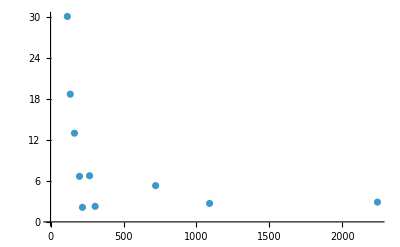

```mathematica
Cnnbar=(ρm-πm)/(16/3+16);
Csnbar=(Kms-Km)/(16/3+16);
Cssbar=(ϕ-ϕ0)/(16/3+16);
Ccnbar=(Dms-Dm)/(16/3+16);
Ccsbar=(Dsms-Dsm)/(16/3+16);
Cccbar=(Jψ-ηc)/(16/3+16);
Cbnbar=(Bmsn-Bmu)/(16/3+16);
Cbsbar=(Bsms-Bsm)/(16/3+16);
Cbcbar=(Bcms-Bcm)/(16/3+16);
Cbbbar=(Υ-ηb)/(16/3+16);

γA=0.85;
Cnn=Cnnbar*γA;
Csn=Csnbar*γA;
Css=Cssbar*γA;
Ccn=Ccnbar*γA;
Ccs=Ccsbar*γA;
Ccc=Cccbar*γA;
Cbn=Cbnbar*γA;
Cbs=Cbsbar*γA;
Cbc=Cbcbar*γA;
Cbb=Cbbbar*γA;

Print[{"Cnnbar="<>ToString[Cnnbar,FormatType->TraditionalForm],"Csnbar="<>ToString[Csnbar,FormatType->TraditionalForm],"Cssbar="<>ToString[Cssbar,FormatType->TraditionalForm],"Ccnbar="<>ToString[Ccnbar,FormatType->TraditionalForm],"Ccsbar="<>ToString[Ccsbar,FormatType->TraditionalForm],"Cccbar="<>ToString[Cccbar,FormatType->TraditionalForm],"Cbnbar="<>ToString[Cbnbar,FormatType->TraditionalForm],"Cbsbar="<>ToString[Cbsbar,FormatType->TraditionalForm],"Cbcbar="<>ToString[Cbcbar,FormatType->TraditionalForm],"Cbbbar="<>ToString[Cbbbar,FormatType->TraditionalForm]}];
Print[{"Cnn="<>ToString[Cnn,FormatType->TraditionalForm],"Csn="<>ToString[Csn,FormatType->TraditionalForm],"Css="<>ToString[Css,FormatType->TraditionalForm],"Ccn="<>ToString[Ccn,FormatType->TraditionalForm],"Ccs="<>ToString[Ccs,FormatType->TraditionalForm],"Ccc="<>ToString[Ccc,FormatType->TraditionalForm],"Cbn="<>ToString[Cbn,FormatType->TraditionalForm],"Cbs="<>ToString[Cbs,FormatType->TraditionalForm],"Cbc="<>ToString[Cbc,FormatType->TraditionalForm],"Cbb="<>ToString[Cbb,FormatType->TraditionalForm]}];

dataC1={{μnn,Cnnbar},{μsn,Csnbar},{μss,Cssbar},{μcn,Ccnbar},{μcs,Ccsbar},{μcc,Cccbar},{μbn,Cbnbar},{μbs,Cbsbar},{μbc,Cbcbar},{μbb,Cbbbar}};
ListPlot[dataC1]
```

## CMI Inequalities

```mathematica
{"snbar ssbar nnbar"}
ΔCsn0=-16Csnbar-(-16Cssbar-16Cnnbar)/2;
Print["ΔK-(Δϕ0+Δπ)/2="<> ToString[ΔCsn0]];
ΔCsn1=16/3 Csnbar-(16/3 Cssbar+16/3 Cnnbar)/2;
Print["ΔK^*-(Δϕ+Δρ)/2="<> ToString[ΔCsn1]];

{"cnbar ccbar nnbar"}
ΔCcn0=-16Ccnbar-(-16Cccbar-16Cnnbar)/2;
Print["ΔD-(Δηc+Δπ)/2="<> ToString[ΔCcn0]];
ΔCcn1=16/3 Ccnbar-(16/3 Cccbar+16/3 Cnnbar)/2;
Print["ΔD^*-(ΔJψ+Δρ)/2="<> ToString[ΔCcn1]];

{"bnbar bbbar nnbar"}
ΔCbn0=-16Cbnbar-(-16Cbbbar-16Cnnbar)/2;
Print["ΔB-(Δηb+Δπ)/2="<> ToString[ΔCbn0]];
ΔCbn1=16/3 Cbnbar-(16/3 Cbbbar+16/3 Cnnbar)/2;
Print["ΔB^*-(ΔΥ+Δρ)/2="<> ToString[ΔCbn1]];

{"csbar ccbar ssbar"}
ΔCcs0=-16Ccsbar-(-16Cccbar-16Cssbar)/2;
Print["ΔDs-(Δηc+Δϕ0)/2="<> ToString[ΔCcs0]];
ΔCcs1=16/3 Ccsbar-(16/3 Cccbar+16/3 Cssbar)/2;
Print["ΔDs^*-(ΔJψ+Δϕ)/2="<> ToString[ΔCcs1]];

{"bsbar bbbar ssbar"}
ΔCbs0=-16Cbsbar-(-16Cbbbar-16Cssbar)/2;
Print["ΔBs-(Δηb+Δϕ0)/2="<> ToString[ΔCbs0]];
ΔCbs1=16/3 Cbsbar-(16/3 Cbbbar+16/3 Cssbar)/2;
Print["ΔBs^*-(ΔΥ+Δϕ)/2="<> ToString[ΔCbs1]];

{"bcbar bbbar ccbar"}
ΔCbc0=-16Cbcbar-(-16Cbbbar-16Cccbar)/2;
Print["ΔBc-(Δηb+Δηc)/2="<> ToString[ΔCbc0]];
ΔCbc1=16/3 Cbcbar-(16/3 Cbbbar+16/3 Cccbar)/2;
Print["ΔBc^*-(ΔΥ+ΔJψ)/2="<> ToString[ΔCbc1]];

{"csn css cnn"}
ΔCcsn1=8/3 Csn-16/3 Ccn-16/3 Ccs-(8/3 Css-32/3 Ccs+8/3 Cnn-32/3 Ccn)/2;
Print["ΔΞc'-(ΔΩc+ΔΣc)/2="<> ToString[ΔCcsn1]];
ΔCcsn3=8/3 Ccs+8/3 Ccn+8/3 Csn-(16/3 Ccs+8/3 Css+16/3 Ccn+8/3 Cnn)/2;
Print["ΔΞc^*-(ΔΩc^*+ΔΣc^*)/2="<> ToString[ΔCcsn3]];

{"bsn bss bnn"}
ΔCbsn1=8/3 Csn-16/3 Cbn-16/3 Cbs-(8/3 Css-32/3 Cbs+8/3 Cnn-32/3 Cbn)/2;
Print["ΔΞb'-(ΔΩb+ΔΣb)/2="<> ToString[ΔCbsn1]];
ΔCbsn3=8/3 Cbs+8/3 Cbn+8/3 Csn-(16/3 Cbs+8/3 Css+16/3 Cbn+8/3 Cnn)/2;
Print["ΔΞb^*-(ΔΩb^*+ΔΣb^*)/2="<> ToString[ΔCbsn3]];

{"nsc nss ncc"}
ΔCnsc1=8/3 Csn-16/3 Ccn-16/3 Ccs-(8/3 Css-32/3 Csn+8/3 Ccc-32/3 Ccn)/2;
Print["ΔΞc'-(ΔΞ+ΔΞcc)/2="<> ToString[ΔCnsc1]];
ΔCnsc3=8/3 Csn+8/3 Ccn+8/3 Ccs-(16/3 Csn+8/3 Css+16/3 Ccn+8/3 Ccc)/2;
Print["ΔΞc^*-(ΔΞ^*+ΔΞcc^*)/2="<> ToString[ΔCnsc3]];

{"nsb nss nbb"}
ΔCnsb1=8/3 Csn-16/3 Cbn-16/3 Cbs-(8/3 Css-32/3 Csn+8/3 Cbb-32/3 Cbn)/2;
Print["ΔΞb'-(ΔΞ+ΔΞbb)/2="<> ToString[ΔCnsb1]];
ΔCnsb3=8/3 Csn+8/3 Cbn+8/3 Cbs-(16/3 Csn+8/3 Css+16/3 Cbn+8/3 Cbb)/2;
Print["ΔΞb^*-(ΔΞ^*+ΔΞbb^*)/2="<> ToString[ΔCnsb3]];

{"ssn sss snn"}
ΔCssn3=8/3 Css+16/3 Csn-(8Css+16/3 Csn+8/3 Cnn)/2;
Print["ΔΞ^*-(ΔΩ+ΔΣ^*)/2="<> ToString[ΔCssn3]];

{"ssc sss scc"}
ΔCssc3=8/3 Css+16/3 Ccs-(8Css+16/3 Ccs+8/3 Ccc)/2;
Print["ΔΩc^*-(ΔΩ+ΔΩcc^*)/2="<> ToString[ΔCssc3]];

{"ssb sss sbb"}
ΔCssb3=8/3 Css+16/3 Cbs-(8Css+16/3 Cbs+8/3 Cbb)/2;
Print["ΔΩb^*-(ΔΩ+ΔΩbb^*)/2="<> ToString[ΔCssb3]];

{"ccn ccc cnn"}
ΔCccn3=8/3 Ccc+16/3 Ccn-(8Ccc+16/3 Ccn+8/3 Cnn)/2;
Print["ΔΞcc^*-(ΔΩccc+ΔΣc^*)/2="<> ToString[ΔCccn3]];

{"ccs ccc css"}
ΔCccs3=8/3 Ccc+16/3 Ccs-(8Ccc+16/3 Ccs+8/3 Css)/2;
Print["ΔΩcc^*-(ΔΩccc+ΔΩc^*)/2="<> ToString[ΔCccs3]];

{"ccb ccc cbb"}
ΔCccb3=8/3 Ccc+16/3 Cbc-(8Ccc+16/3 Cbc+8/3 Cbb)/2;
Print["ΔΩccb^*-(ΔΩccc+ΔΩcbb^*)/2="<> ToString[ΔCccb3]];

{"bbn bbb bnn"}
ΔCbbn3=8/3 Cbb+16/3 Cbn-(8Cbb+16/3 Cbn+8/3 Cnn)/2;
Print["ΔΞbb^*-(ΔΩbbb+ΔΣb^*)/2="<> ToString[ΔCbbn3]];

{"bbs bbb bss"}
ΔCbbs3=8/3 Cbb+16/3 Cbs-(8Cbb+16/3 Cbs+8/3 Css)/2;
Print["ΔΩbb^*-(ΔΩbbb+ΔΩb^*)/2="<> ToString[ΔCbbs3]];

{"bbc bbb bcc"}
ΔCbbc3=8/3 Cbb+16/3 Cbc-(8Cbb+16/3 Cbc+8/3 Ccc)/2;
Print["ΔΩbbc^*-(ΔΩbbb+ΔΩbcc^*)/2="<> ToString[ΔCbbc3]];

{"bcn bcc bnn"}
ΔCbcn1=8/3 Cbc-16/3 Cbn-16/3 Ccn-(8/3 Ccc-32/3 Cbc+8/3 Cnn-32/3 Cbn)/2;
Print["ΔΞbc-(ΔΩbcc+ΔΣb)/2="<> ToString[ΔCbcn1]];
ΔCbcn3=8/3 Cbc+8/3 Cbn+8/3 Ccn-(16/3 Cbc+8/3 Ccc+16/3 Cbn+8/3 Cnn)/2;
Print["ΔΞbc^*-(ΔΩbcc^*+ΔΣb^*)/2="<> ToString[ΔCbcn3]];

{"bcs bcc bss"}
ΔCbcs1=8/3 Cbc-16/3 Cbs-16/3 Ccs-(8/3 Ccc-32/3 Cbc+8/3 Css-32/3 Cbs)/2;
Print["ΔΩbc-(ΔΩbcc+ΔΩb)/2="<> ToString[ΔCbcs1]];
ΔCbcs3=8/3 Cbc+8/3 Cbs+8/3 Ccs-(16/3 Cbc+8/3 Ccc+16/3 Cbs+8/3 Css)/2;
Print["ΔΩbc^*-(ΔΩbcc^*+ΔΩb^*)/2="<> ToString[ΔCbcs3]];

{"csn ccc sss nnn"}
Δ3Ccsn3=8/3 Ccs+8/3 Ccn+8/3 Csn-(8Ccc+8Css+8Cnn)/3;
Print["ΔΞc^*-(ΔΩccc+ΔΩ+ΔΔ)/3="<> ToString[Δ3Ccsn3]];

{"bsn bbb sss nnn"}
Δ3Cbsn3=8/3 Cbs+8/3 Cbn+8/3 Csn-(8Cbb+8Css+8Cnn)/3;
Print["ΔΞb^*-(ΔΩbbb+ΔΩ+ΔΔ)/3="<> ToString[Δ3Cbsn3]];

{"bcn bbb ccc nnn"}
Δ3Cbcn3=8/3 Cbc+8/3 Cbn+8/3 Ccn-(8Cbb+8Ccc+8Cnn)/3;
Print["ΔΞbc^*-(ΔΩbbb+ΔΩccc+ΔΔ)/3="<> ToString[Δ3Cbcn3]];

{"bcs bbb ccc sss"}
Δ3Cbcs3=8/3 Cbc+8/3 Cbs+8/3 Ccs-(8Cbb+8Ccc+8Css)/3;
Print["ΔΩbc^*-(ΔΩbbb+ΔΩccc+ΔΩ)/3="<> ToString[Δ3Cbcs3]];
```

{snbar ssbar nnbar}

ΔK-(Δϕ0+Δπ)/2=45.3075

ΔK^*-(Δϕ+Δρ)/2=-15.1025

{cnbar ccbar nnbar}

ΔD-(Δηc+Δπ)/2=175.965

ΔD^*-(ΔJψ+Δρ)/2=-58.655

{bnbar bbbar nnbar}

ΔB-(Δηb+Δπ)/2=229.17

ΔB^*-(ΔΥ+Δρ)/2=-76.39

{csbar ccbar ssbar}

ΔDs-(Δηc+Δϕ0)/2=38.16

ΔDs^*-(ΔJψ+Δϕ)/2=-12.72

{bsbar bbbar ssbar}

ΔBs-(Δηb+Δϕ0)/2=90.4125

ΔBs^*-(ΔΥ+Δϕ)/2=-30.1375

{bcbar bbbar ccbar}

ΔBc-(Δηb+Δηc)/2=22.3275

ΔBc^*-(ΔΥ+ΔJψ)/2=-7.4425

{csn css cnn}

ΔΞc'-(ΔΩc+ΔΣc)/2=-6.41856

ΔΞc^*-(ΔΩc^*+ΔΣc^*)/2=-6.41856

{bsn bss bnn}

ΔΞb'-(ΔΩb+ΔΣb)/2=-6.41856

ΔΞb^*-(ΔΩb^*+ΔΣb^*)/2=-6.41856

{nsc nss ncc}

ΔΞc'-(ΔΞ+ΔΞcc)/2=75.5884

ΔΞc^*-(ΔΞ^*+ΔΞcc^*)/2=-5.406

{nsb nss nbb}

ΔΞb'-(ΔΞ+ΔΞbb)/2=98.5851

ΔΞb^*-(ΔΞ^*+ΔΞbb^*)/2=-12.8084

{ssn sss snn}

ΔΞ^*-(ΔΩ+ΔΣ^*)/2=-6.41856

{ssc sss scc}

ΔΩc^*-(ΔΩ+ΔΩcc^*)/2=-5.406

{ssb sss sbb}

ΔΩb^*-(ΔΩ+ΔΩbb^*)/2=-12.8084

{ccn ccc cnn}

ΔΞcc^*-(ΔΩccc+ΔΣc^*)/2=-24.9284

{ccs ccc css}

ΔΩcc^*-(ΔΩccc+ΔΩc^*)/2=-5.406

{ccb ccc cbb}

ΔΩccb^*-(ΔΩccc+ΔΩcbb^*)/2=-3.16306

{bbn bbb bnn}

ΔΞbb^*-(ΔΩbbb+ΔΣb^*)/2=-32.4657

{bbs bbb bss}

ΔΩbb^*-(ΔΩbbb+ΔΩb^*)/2=-12.8084

{bbc bbb bcc}

ΔΩbbc^*-(ΔΩbbb+ΔΩbcc^*)/2=-3.16306

{bcn bcc bnn}

ΔΞbc-(ΔΩbcc+ΔΣb)/2=-51.8564

ΔΞbc^*-(ΔΩbcc^*+ΔΣb^*)/2=-24.9284

{bcs bcc bss}

ΔΩbc-(ΔΩbcc+ΔΩb)/2=-32.9205

ΔΩbc^*-(ΔΩbcc^*+ΔΩb^*)/2=-5.406

{csn ccc sss nnn}

ΔΞc^*-(ΔΩccc+ΔΩ+ΔΔ)/3=-36.7529

{bsn bbb sss nnn}

ΔΞb^*-(ΔΩbbb+ΔΩ+ΔΔ)/3=-51.6927

{bcn bbb ccc nnn}

ΔΞbc^*-(ΔΩbbb+ΔΩccc+ΔΔ)/3=-60.5572

{bcs bbb ccc sss}

ΔΩbc^*-(ΔΩbbb+ΔΩccc+ΔΩ)/3=-21.3775

## Binding Fittings

{Bnnbar=0.,Bsnbar=0.,Bssbar=-26.585,Bcnbar=0.,Bbnbar=0.,Bcsbar=-75.9775,Bbsbar=-91.035,Bccbar=-258.85,Bbcbar=-351.982,Bbbbar=-566.8}

{Bnn=0.,Bsn=0.,Bss=-13.2925,Bcn=0.,Bbn=0.,Bcs=-37.9888,Bbs=-45.5175,Bcc=-129.425,Bbc=-175.991,Bbb=-283.4}

-38.7495-0.0000294692 μ^2-79.1351 Log[μ^2/40000]

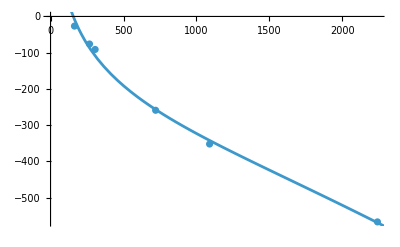

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{1.26623}

```mathematica
(* spin-averaged mCsses *)
Mnnbar=(3ρm+πm)/4;Msnbar=(3Kms+Km)/4;Mssbar=(3ϕ+ϕ0)/4;Mcnbar=(3Dms+Dm)/4;Mcsbar=(3Dsms+Dsm)/4;Mccbar=(3Jψ+ηc)/4;Mbnbar=(3Bms+Bm)/4;Mbsbar=(3Bsms+Bsm)/4;Mbcbar=(3Bcms+Bcm)/4;Mbbbar=(3Υ+ηb)/4;

Bnnbar=Mnnbar-2Mnnbar+Mnnbar;
Bsnbar=Msnbar-Msnbar-Mnnbar+Mnnbar;
Bssbar=Mssbar-2Msnbar+Mnnbar;
Bcnbar=Mcnbar-Mcnbar-Mnnbar+Mnnbar;
Bbnbar=Mbnbar-Mbnbar-Mnnbar+Mnnbar;
Bcsbar=Mcsbar-Mcnbar-Msnbar+Mnnbar;Bbsbar=Mbsbar-Mbnbar-Msnbar+Mnnbar;Bccbar=Mccbar-2Mcnbar+Mnnbar;Bbcbar=Mbcbar-Mbnbar-Mcnbar+Mnnbar;Bbbbar=Mbbbar-2Mbnbar+Mnnbar;

γB=1/2;
Bnn=Bnnbar*γB;
Bsn=Bsnbar*γB;
Bss=Bssbar*γB;
Bcn=Bcnbar*γB;
Bbn=Bbnbar*γB;
Bcs=Bcsbar*γB;
Bbs=Bbsbar*γB;
Bcc=Bccbar*γB;
Bbc=Bbcbar*γB;
Bbb=Bbbbar*γB;

Print[{"Bnnbar="<>ToString[Bnnbar],"Bsnbar="<>ToString[Bsnbar],"Bssbar="<>ToString[Bssbar],"Bcnbar="<>ToString[Bcnbar],"Bbnbar="<>ToString[Bbnbar],"Bcsbar="<>ToString[Bcsbar],"Bbsbar="<>ToString[Bbsbar],"Bccbar="<>ToString[Bccbar],"Bbcbar="<>ToString[Bbcbar],"Bbbbar="<>ToString[Bbbbar]}];
Print[{"Bnn="<>ToString[Bnn],"Bsn="<>ToString[Bsn],"Bss="<>ToString[Bss],"Bcn="<>ToString[Bcn],"Bbn="<>ToString[Bbn],"Bcs="<>ToString[Bcs],"Bbs="<>ToString[Bbs],"Bcc="<>ToString[Bcc],"Bbc="<>ToString[Bbc],"Bbb="<>ToString[Bbb]}];

dataB1={{μbb,Bbbbar},{μbc,Bbcbar},{μcc,Bccbar},{μbs,Bbsbar},{μcs,Bcsbar},{μss,Bssbar}};
ΛQ=200;
fitB1=Fit[dataB1,{1,(μ/ΛQ)^2,Log[(μ/ΛQ)^2]},μ]
Show[ListPlot[dataB1],Plot[fitB1,{μ,100,2300}]]
1000/(5.067μ)/.{Solve[fitB1==0,μ][[2]]}
```

## Binding Inequalities

```mathematica
(* mesons *)
ΔBsn=Bsnbar-(Bssbar+Bnnbar)/2;Print["Bsnbar-(Bnnbar+Bssbar)/2="<> ToString[ΔBsn]];
ΔBcn=Bcnbar-(Bccbar+Bnnbar)/2;Print["Bcnbar-(Bnnbar+Bccbar)/2="<> ToString[ΔBcn]];
ΔBbn=Bbnbar-(Bbbbar+Bnnbar)/2;Print["Bbnbar-(Bnnbar+Bbbbar)/2="<> ToString[ΔBbn]];
ΔBcs=Bcsbar-(Bccbar+Bssbar)/2;Print["Bcsbar-(Bssbar+Bccbar)/2="<> ToString[ΔBcs]];
ΔBbs=Bbsbar-(Bbbbar+Bssbar)/2;Print["Bbsbar-(Bssbar+Bbbbar)/2="<> ToString[ΔBbs]];
ΔBbc=Bbcbar-(Bbbbar+Bccbar)/2;Print["Bbcbar-(Bccbar+Bbbbar)/2="<> ToString[ΔBbc]];
```

Bsnbar-(Bnnbar+Bssbar)/2=13.2925

Bcnbar-(Bnnbar+Bccbar)/2=129.425

Bbnbar-(Bnnbar+Bbbbar)/2=283.4

Bcsbar-(Bssbar+Bccbar)/2=66.74

Bbsbar-(Bssbar+Bbbbar)/2=205.657

Bbcbar-(Bccbar+Bbbbar)/2=60.8425

```mathematica
(* baryons *)
Bnnn=3Bnn;
Bnns=Bnn+2Bsn;
Bnnc=Bnn+2Bcn;
Bnnb=Bnn+2Bbn;
Bssn=Bss+2Bsn;
Bsss=3Bss;
Bssc=Bss+2Bcs;
Bssb=Bss+2Bbs;
Bcsn=Bcs+Bcn+Bsn;
Bccn=Bcc+2Bcn;
Bccs=Bcc+2Bcs;
Bccc=3Bcc;
Bccb=Bcc+2Bbc;
Bbsn=Bbs+Bbn+Bsn;
Bbcn=Bbc+Bbn+Bcn;
Bbcs=Bbc+Bbs+Bcs;
Bbbn=Bbb+2Bbn;
Bbbs=Bbb+2Bbs;
Bbbc=Bbb+2Bbc;
Bbbb=3Bbb;
ΔBnsc=Bcsn-(Bssn+Bccn)/2;Print["Bnsc-(Bnss+Bncc)/2="<> ToString[ΔBnsc]];
ΔBnsb=Bbsn-(Bssn+Bbbn)/2;Print["Bnsb-(Bnss+Bnbb)/2="<> ToString[ΔBnsb]];
ΔBssn=Bssn-(Bsss+Bnns)/2;Print["Bssn-(Bsss+Bsnn)/2="<> ToString[ΔBssn]];
ΔBssc=Bssc-(Bsss+Bccs)/2;Print["Bssc-(Bsss+Bscc)/2="<> ToString[ΔBssc]];
ΔBssb=Bssb-(Bsss+Bbbs)/2;Print["Bssb-(Bsss+Bsbb)/2="<> ToString[ΔBssb]];
ΔBcsn=Bcsn-(Bssc+Bnnc)/2;Print["Bcsn-(Bcss+Bcnn)/2="<> ToString[ΔBcsn]];
ΔBccn=Bccn-(Bnnc+Bccc)/2;Print["Bccn-(Bccc+Bcnn)/2="<> ToString[ΔBccn]];
ΔBccs=Bccs-(Bssc+Bccc)/2;Print["Bccs-(Bccc+Bcss)/2="<> ToString[ΔBccs]];
ΔBccb=Bccb-(Bccc+Bbbc)/2;Print["Bccb-(Bccc+Bcbb)/2="<> ToString[ΔBccb]];
ΔBbsn=Bbsn-(Bssb+Bnnb)/2;Print["Bbsn-(Bbss+Bbnn)/2="<> ToString[ΔBbsn]];
ΔBbcn=Bbcn-(Bccb+Bnnb)/2;Print["Bbcn-(Bbcc+Bbnn)/2="<> ToString[ΔBbcn]];
ΔBbcs=Bbcs-(Bccb+Bssb)/2;Print["Bbcs-(Bbcc+Bbss)/2="<> ToString[ΔBbcs]];
ΔBbbn=Bbbn-(Bnnb+Bbbb)/2;Print["Bbbn-(Bbbb+Bbnn)/2="<> ToString[ΔBbbn]];
ΔBbbs=Bbbs-(Bssb+Bbbb)/2;Print["Bbbs-(Bbbb+Bbss)/2="<> ToString[ΔBbbs]];
ΔBbbc=Bbbc-(Bccb+Bbbb)/2;Print["Bbbc-(Bbbb+Bbcc)/2="<> ToString[ΔBbbc]];
Δ3Bcsn=Bcsn-(Bccc+Bsss+Bnnn)/3;Print["Bcsn-(Bccc+Bsss+Bnnn)/3="<> ToString[Δ3Bcsn]];
Δ3Bbsn=Bbsn-(Bbbb+Bsss+Bnnn)/3;Print["Bbsn-(Bbbb+Bsss+Bnnn)/3="<> ToString[Δ3Bbsn]];
Δ3Bbcn=Bbcn-(Bbbb+Bccc+Bnnn)/3;Print["Bbcn-(Bbbb+Bccc+Bnnn)/3="<> ToString[Δ3Bbcn]];
Δ3Bbcs=Bbcs-(Bbbb+Bccc+Bsss)/3;Print["Bbcs-(Bbbb+Bccc+Bsss)/3="<> ToString[Δ3Bbcs]];
```

Bnsc-(Bnss+Bncc)/2=33.37

Bnsb-(Bnss+Bnbb)/2=102.829

Bssn-(Bsss+Bsnn)/2=6.64625

Bssc-(Bsss+Bscc)/2=33.37

Bssb-(Bsss+Bsbb)/2=102.829

Bcsn-(Bcss+Bcnn)/2=6.64625

Bccn-(Bccc+Bcnn)/2=64.7125

Bccs-(Bccc+Bcss)/2=33.37

Bccb-(Bccc+Bcbb)/2=30.4213

Bbsn-(Bbss+Bbnn)/2=6.64625

Bbcn-(Bbcc+Bbnn)/2=64.7125

Bbcs-(Bbcc+Bbss)/2=33.37

Bbbn-(Bbbb+Bbnn)/2=141.7

Bbbs-(Bbbb+Bbss)/2=102.829

Bbbc-(Bbbb+Bbcc)/2=30.4213

Bcsn-(Bccc+Bsss+Bnnn)/3=104.729

Bbsn-(Bbbb+Bsss+Bnnn)/3=251.175

Bbcn-(Bbbb+Bccc+Bnnn)/3=236.834

Bbcs-(Bbbb+Bccc+Bsss)/3=166.62

## Experimental Proof

```mathematica
system={"K^*-(ϕ+ρ)/2","D^*-(Jψ+ρ)/2","D-(Jψ+π)/2","B^*-(Υ+ρ)/2","B-(ηb+π)/2","Ds^*-(Jψ+ϕ)/2","Bs^*-(Υ+ϕ)/2","Bc^*-(Υ+Jψ)/2","Bc-(ηb+ηc)/2","Ξ^*-(Ω+Σ^*)/2","Ξc^*-(Ωc^*+Σc^*)/2","Ξc'-(Ωc+Σc)/2","Ξc'-(Ξ+Ξcc)/2","Ξb'-(Ωb+Σb)/2"};
ΔM={ΔMsn1,ΔMcn1,ΔMcn0,ΔMbn1,ΔMbn0,ΔMcs1,ΔMbs1,ΔMbc1,ΔMbc0,ΔMssn3,ΔMcsn3,ΔMcsn1,ΔMusc1,ΔMbsn1};
ΔBC={ΔBsn+ΔCsn1,ΔBcn+ΔCcn1,ΔBcn+ΔCcn0,ΔBbn+ΔCbn1,ΔBbn+ΔCbn0,ΔBcs+ΔCcs1,ΔBbs+ΔCbs1,ΔBbc+ΔCbc1,ΔBbc+ΔCbc0,ΔBssn+ΔCssn3,ΔBcsn+ΔCcsn3,ΔBcsn+ΔCcsn1,ΔBnsc+ΔCnsc1,ΔBbsn+ΔCbsn1};
Transpose[{Join[{"system"},system],Join[{"ΔM"},ΔM],Join[{"ΔB+ΔC"},ΔBC]}]//MatrixForm

sum=0;
For[i=1,i<=Length[ΔM],i++,
sum=sum+(ΔM[[i]]-ΔBC[[i]])^2;]
Print["σ="<>ToString[(sum/Length[ΔM])^(1/2)]<>"MeV"]
```

(system | ΔM | ΔB+ΔC
K^*-(ϕ+ρ)/2 | -3.75 | -1.81
D^*-(Jψ+ρ)/2 | 72.475 | 70.77
D-(Jψ+π)/2 | 307.8 | 305.39
B^*-(Υ+ρ)/2 | 206.93 | 207.01
B-(ηb+π)/2 | 512.65 | 512.57
Ds^*-(Jψ+ϕ)/2 | 54.02 | 54.02
Bs^*-(Υ+ϕ)/2 | 175.52 | 175.52
Bc^*-(Υ+Jψ)/2 | 53.4 | 53.4
Bc-(ηb+ηc)/2 | 83.17 | 83.17
Ξ^*-(Ω+Σ^*)/2 | 4.675 | 0.227687
Ξc^*-(Ωc^*+Σc^*)/2 | 3.4575 | 0.227687
Ξc'-(Ωc+Σc)/2 | 3.92 | 0.227687
Ξc'-(Ξ+Ξcc)/2 | 109.97 | 108.958
Ξb'-(Ωb+Σb)/2 | 4.6 | 0.227687)

σ=2.33721MeV

## Prediction

```mathematica
system={"Ξc^*-(Ξ^*+Ξcc^*)/2","Ξb^*-(Ξ^*+Ξbb^*)/2","Ξb^*-(Ωb^*+Σb^*)/2","Ξb'-(Ξ+Ξbb)/2","Ωc^*-(Ω+Ωcc^*)/2","Ωb^*-(Ω+Ωbb^*)/2","Ξcc^*-(Ωccc+Σc^*)/2","Ωcc^*-(Ωccc+Ωc^*)/2","Ωccb^*-(Ωccc+Ωcbb^*)/2","Ξbb^*-(Ωbbb+Σb^*)/2","Ωbb^*-(Ωbbb+Ωb^*)/2","Ωbbc^*-(Ωbbb+Ωbcc^*)/2","Ξbc^*-(Ωbcc^*+Σb^*)/2","Ξbc-(Ωbcc+Σb)/2","Ωbc^*-(Ωbcc^*+Ωb^*)/2","Ωbc-(Ωbcc+Ωb)/2","Ξc^*-(Ωccc+Ω+Δ)/3","Ξb^*-(Ωbbb+Ω+Δ)/3","Ξbc^*-(Ωbbb+Ωccc+Δ)/3","Ωbc^*-(Ωbbb+Ωccc+Ω)/3"};
ΔBC={ΔBnsc+ΔCnsc3,ΔBnsb+ΔCnsb3,ΔBbsn+ΔCbsn3,ΔBnsb+ΔCnsb1,ΔBssc+ΔCssc3,ΔBssb+ΔCssb3,ΔBccn+ΔCccn3,ΔBccs+ΔCccs3,ΔBccb+ΔCccb3,ΔBbbn+ΔCbbn3,ΔBbbs+ΔCbbs3,ΔBbbc+ΔCbbc3,ΔBbcn+ΔCbcn3,ΔBbcn+ΔCbcn1,ΔBbcs+ΔCbcs3,ΔBbcs+ΔCbcs1,Δ3Bcsn+Δ3Ccsn3,Δ3Bbsn+Δ3Cbsn3,Δ3Bbcn+Δ3Cbcn3,Δ3Bbcs+Δ3Cbcs3};
Transpose[{Join[{"system"},system],Join[{"ΔB+ΔC"},ΔBC]}]//MatrixForm

Ξccs=2(Ξcs-(ΔBnsc+ΔCnsc3))-Ξs;
Ξcc=2(Ξcp-(ΔBnsc+ΔCnsc1))-Ξ;
Ξbbs=2(Ξbs-(ΔBnsb+ΔCnsb3))-Ξs;
Ξbb=2(Ξbp-(ΔBnsb+ΔCnsb1))-Ξ;
Ωbs=2(Ξbs-(ΔBbsn+ΔCbsn3))-Σbs;
Ωccs=2(Ωcs-(ΔBssc+ΔCssc3))-Ω;
Ωccc=3(Ξcs-(Δ3Bcsn+Δ3Ccsn3))-Ω-Δ;
Ωbbb=3(Ξbs-(Δ3Bbsn+Δ3Cbsn3))-Ω-Δ;
Print[{"Ξcc^*="<>ToString[Ξccs],"Ξcc="<>ToString[Ξcc],"Ξbb^*="<>ToString[Ξbbs],"Ξbb="<>ToString[Ξbb],"Ωb^*="<>ToString[Ωbs],"Ωcc^*="<>ToString[Ωccs],"Ωccc="<>ToString[Ωccc],"Ωbbb="<>ToString[Ωbbb]}]
```

(system | ΔB+ΔC
Ξc^*-(Ξ^*+Ξcc^*)/2 | 27.964
Ξb^*-(Ξ^*+Ξbb^*)/2 | 90.0203
Ξb^*-(Ωb^*+Σb^*)/2 | 0.227687
Ξb'-(Ξ+Ξbb)/2 | 201.414
Ωc^*-(Ω+Ωcc^*)/2 | 27.964
Ωb^*-(Ω+Ωbb^*)/2 | 90.0203
Ξcc^*-(Ωccc+Σc^*)/2 | 39.7841
Ωcc^*-(Ωccc+Ωc^*)/2 | 27.964
Ωccb^*-(Ωccc+Ωcbb^*)/2 | 27.2582
Ξbb^*-(Ωbbb+Σb^*)/2 | 109.234
Ωbb^*-(Ωbbb+Ωb^*)/2 | 90.0203
Ωbbc^*-(Ωbbb+Ωbcc^*)/2 | 27.2582
Ξbc^*-(Ωbcc^*+Σb^*)/2 | 39.7841
Ξbc-(Ωbcc+Σb)/2 | 12.8561
Ωbc^*-(Ωbcc^*+Ωb^*)/2 | 27.964
Ωbc-(Ωbcc+Ωb)/2 | 0.4495
Ξc^*-(Ωccc+Ω+Δ)/3 | 67.9758
Ξb^*-(Ωbbb+Ω+Δ)/3 | 199.482
Ξbc^*-(Ωbbb+Ωccc+Δ)/3 | 176.277
Ωbc^*-(Ωbbb+Ωccc+Ω)/3 | 145.243)

{Ξcc^*=3704.59,Ξcc=3624.62,Ξbb^*=10198.8,Ξbb=10152.3,Ωb^*=6077.67,Ωcc^*=3803.42,Ωccc=4830.1,Ωbbb=14363.1}